### Features to be added

#### Implement automatic adjustment of the frequency resolution of the simulation

freqStep is the simulation parameter that decides the resolution of the frequency band of the ESR. Currently, this frequency step is kept constant for the duration of the simulation. One way to improve the performance of the simulation would be to dynamically adjust the frequency step during the run.

We’d want to have a higher resolution for frequencies in the frequency-ranges close to resonance, and a lower resolution for regions in the frequency-band that are off-resonance. We can directly see the potential benefits of this feature by inspecting the following example of a simulation run:

-Graphics-

We see that the the frequency-resolution is unnecessarily high in the off-resonance regions.

One possible method to implement this feature would be to make freqStep a function of the gradient of the ESR curve.

#### Implement automatic adjustment of the length of the solutions of the quantum master equation

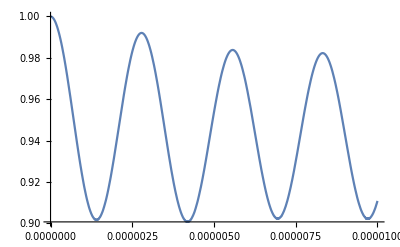
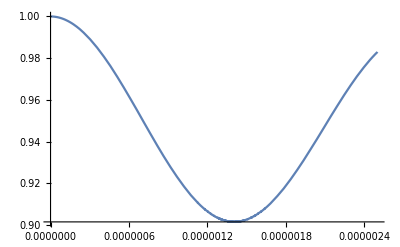
Similarly, another performance-boosting feature would be to make the simulation length tEnd - tStart  a dynamic variable.

It is important that the simulation length to be sufficiently long during resonance, as otherwise the time-averaged probabilities can get distorted. For example, consider the following graph of the system undergoing Rabi oscillation:

-Graphics-

It is obvious that if the simulation was too short

-Graphics-

The accuracy of the time-averaged probability would suffer. On the other hand, in off-resonance, we do not need very long simulation times. Thus a similar feature could be implemented, as for the frequency resolution.